```mathematica
SetOptions[$FrontEnd,DynamicEvaluationTimeout->Infinity]
```

# Quadratic Gravity And Scalar Dark Matter In A Gravitational Wave Context.

## Hontas Farmer and Shane Larson

We present, in the form of an interactive Mathematica notebook, a model of classical quadratic gravity with a massive scalar field in the context of extreme mass ratio in spirals which could be tested with the future Laser Interferometer Space Antenna.   This document is meant to accommodate a peer reviewed publication and is where the analysis in that publication was done. 

The Lagrangian is written, field equations derived, then solved exactly without approximation.  Further computational investigation and evaluation was done to evaluate the consistency of the result with LIGO observations.  The result is a model which does not disturb the classic solar system test of general relativity but which in extreme conditions models cosmological behavior, and which would have LISA observable consequences in the context of an extreme mass ratio in spiral. Quadratic gravity theories are some of the best candidates for alternative gravity models which have not been eliminated by LIGO observation.  For example Starobinsky gravity, an inflationary model that fits available Planck data, while in the study of quantum gravity quadratic terms lead to a renormalization model. Given that data two parameters that appear in this model are precisely constrained to small but non-zero values.   Investigation of the EMRI environment may result in this model being validated or refuted by experiment as this paper shows.  

This Mathematica notebook is meant as a supplement to formal publication.  It includes details which are not appropriate for, or not possible in, the format of a journal paper.  For example some of the Mathematica code and results, if fully expanded make this document a few times longer, and there are interactive plots.

## Introduction

Alternative gravitational theories to general relativity have enjoyed
a long history of theoretical development and subsequent testing against
experiment. Many have been strongly constrained from astrophysical
or solar system tests (\citep{2018JCAP...12..030K}), and more recently
by gravitational-wave analysis of LIGO events (\citep{2019PhRvD..99d4056J}).
Quadratic gravity theories, which contain terms such as Ricci scalar
squared, are some of the best candidates for alternative gravity models,
which have not been strongly eliminated through experimental efforts.
For example, Starobinsky gravity is an inflationary model that fits
available Planck data; in the study of quantum gravity the quadratic
terms in the Starobinsky theory lead to a re-normalization model.
For these reasons, quadratic models are very important and of great
observational and theoretical interest. It has been proposed that
observations by the Laser Interferometer Space Antenna (LISA) of Extreme
Mass Ratio Inspirals (EMRIs) could be used to probe for new physics.
\citep{Arun2022} \citep{2020GReGr..52...81B}

This paper examines an $F(R)$ gravity model that combines the simplest
quadratic gravity of Starobinsky gravity, which has been studied extensively
in cosmology, with an ultralight scalar field\citep{1980PhLB...91...99S,1987quco.book..130S,1985PhRvD..32.2511V}.
The low mass scalar field can be interpreted as a candidate for dark
matter, such as fuzzy dark matter or axion dark matter \citep{2000PhRvL..85.1158H,2020MNRAS.498.3616A,2009NJPh...11j5008D}.
These models are typically analyzed in a parameterized post-Einsteinian
(PPE) framework \citep{2020GReGr..52...81B,2022arXiv220306240B},
which is a generalization of the parameterized post-Newtonian (PPN)
formalism\citep{2014PhRvD..90j4010L,2017PhRvD..96h9901L,2011PhRvD..84f2003C,2009PhRvD..80l2003Y}.
The PPE approach allows various computational and approximation methods,
such as extreme mass ratio inspiral (EMRI) kludges \citep{2017PhRvD..96d4005C,2007PhRvD..75b4005B}
that can provide accurate numerical solutions, useful for understanding
how LISA observations can probe and constrain these models.

The work presented here outlines an analytical solution for the field
equations of Starobinsky gravity with a scalar field up to an integral.
It is always pleasant to avail of analytical solutions even if they
are not of simple form. More importantly, solutions that are analytical,
if not truly exact, leave less room for doubt about the outcome when
a theory is put to the test of observation. Another motivation is
that analytic results can be easily manipulated, and they are very
expedient to compute results from when they are embedded in larger
simulations and problems, as we often do in GW physics. The key observation
used to arrive at the analytic result is that the scalar field $\phi$,
if it exists, must be small. Many observations made to search for
such a field indicate that it must be of very low mass \citep{2020PhRvL.125n1101M,2020CQGra..37k5001G,2020EPJC...80..350F,2019JCAP...11..025M,2019PhRvD.100j4061J,2019PhRvD..99l4050K,2019IJMPD..2830012Q,2018PhRvD..98b4038H,2012PhRvD..85j2003Y,1997hep.th....2070D,2019arXiv191201420L}.

Quadratic gravity models have been investigated theoretically for
both static situations and application to cosmology, and in the context
of quantum field theory in curved spacetime, with the common assumption
that the Ricci scalar would take on a small but non-zero constant
value \citep{2011PhRvD..83h4015G,2017PhRvD..95h4025P}. Gravitational
wave physics presents a unique challenge, where the Ricci scalar is
not assumed to be zero or any other constant. We will assume the background
space time due to the Black hole is of zero Ricci curvature but allow
the Ricci curvature due to the gravitational waves to oscillate.

-Graphics-

Here we consider the action

S=∫√-g[F(R)-1/2 g^μν∇_μ ϕ∇_ν ϕ-1/2 mϕ^2]ⅆ^4 x

Where $m$ is the mass of the scalar field $\Phi$, and $F(R)$ is
given as:

F(R)=R+βR^2-ξRϕ^2

Here, $\beta$ and $\xi$ are coupling constants which we are free
to set to any value, but will be chosen
for theoretical reasons . For example setting $\xi$ to 1/6 for conformal
coupling, or choosing it to be close to zero based on physical
observations . The same holds true for $\beta$ .

### Deriving the field equations

The field equations can be derived from the action in Eq.~\ref{eq:Action}
by taking functional/variational derivatives. The immediate result
will be modified Einstein field equations and a modified equation
of motion for a scalar field in curved spacetime with a Starobinsky
term:

F'(R)R_μν-1/2 F(R)g_μν+(g_μν-∇_μ ∇_ν)F'(R)=κ^2 T_μν

(1+2βR-ξϕ^2)R_μν-1/2(R+βR^2-ξRϕ^2)g_μν+(g_μν-∇_μ ∇_ν)(1+2βR-ξϕ^2)=κ^2 T_μν

Gathering the Einstein tensor $G_ {\mu \n u} = R_ {\mu \n u} - \tfrac {1} {2} R g_ {\mu \n u} $ illuminates how various
modifications in this theory factor into the Einstein Equations :

Equation \ref{eq:TensorFieldequations2} can then be traced into a form that
is only in terms of invariants\citep{2012JPhCS.384a2030G,2020CQGra..37k5001G}, yielding:

F'(R)R-2f(R)+3□ F'(R)=κ^2 T

For the f(R) we are studying in this paper take a derivative with respect to R (d/dR as if it was X and this was a 1 D problem.  Strange as that may feel since we know R is itself a function of four space time variables.  That is the simple beauty of working with invariants.) Carrying out this problem as much as possible using the faultless math of Mathematica.

(6 β□- 1+ξ ϕ^2)R-3 ξ □ϕ^2 =κ^2 T

The process of taking the functional derivative of the action for the scalar field phi leads to the field equation for that field.  The result is a set of two field equations which will need to be solved simultaneously to fully solve the problem.

{ (□- 1/(6 β)+ξ/(6 β) ϕ^2)R-ξ/(2β) □ϕ^2 =κ^2/(6 β)T
(□-m^2-ξ R)ϕ=0}

A solution to the above set of equations should not depend on the choice of coordinates. The problem as it stands is formulated in terms of invariant quantities and the solutions should themselves be invariants. When coordinates are chosen, and the correct limits are taken the amplitude of the fields should drop off as 1/r or 1/r^2 .

## Solving the field equations up to an integral, analytically.

To solve these analytically let us consider some extremal cases.  Then using this simplified cases we can assemble an analytical solution.

### Setting the Starobinsky coefficient to zero, β =0

This is not allowed due to the appearance of terms which contain beta in the denominator.

{ (□- 1/(6 0)+ξ/(6 0) ϕ^2)R-ξ/(2 0) □ϕ^2 =κ^2/(6 0)T
(□-m^2-ξ R)ϕ=0}

This would lead to expressions that are undefined mathematically.

### Setting the Ricci scalar to zero, R =0 Case1

Setting R equal to zero causes the field equations to collapse to a simple form.

{ -ξ/(2β) □ϕ^2 =κ^2/(6 β)T
(□-m^2)ϕ=0}

This form of the equations is Ricci vacuum.  The result is that ϕ is described by the Klein-Gordon equation in flat space time.

(□-m^2)ϕ=0

Following the methods of Caroll and basic calculus.  The equation can be simplified by transforming it into a first order equation using an appropriate Killing vector.  Once this is done we get two complex valued equations one for the positive energy states and one for the negative energy states.  The solutions to these give us exponentials which lead to wave functions.   The solution works out to

ϕ=ϕ_0 e^(-ⅈω∫k_μ ⅆ x^μ)+ϕ_1 e^(ⅈω∫k_μ ⅆ x^μ)

In which k_μ is an appropriately chosen Killing vector.

There is a small modification to the stress energy invariant in this case.

T=- (3ξ)/κ^2□ϕ^2

### Setting the Starobinsky coefficient to zero, ϕ =0 Case2

In this case the scalar field does not exist the result is an equation which can be solved by the same methods as used for the Klein-Gordon equation in curved space time.

(□- 1/(6 β))R =κ^2/(6 β)T

The procedure and result are very similar. The difference is there is a recursive term that appears where in the value at one point depends on the value previously.

g_i =e^(-ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i √((κ^2 T)/(6 β))ⅆ x^μ)

g_i^*=e^(ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i √((κ^2 T)/(6 β))ⅆ x^μ)

The solution is then.

R=R_0 e^(-ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i √((κ^2 T)/(6 β))ⅆ x^μ)+R_1 e^(ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i^*√((κ^2 T)/(6 β))ⅆ x^μ)

### Setting the Starobinsky coefficient to zero, ξ =0 Case 3

In this case the equations are decoupled with no explicit interaction between the fields in the field equations.

{ (□- 1/(6 β))R =κ^2/(6 β)T
(□-m^2)ϕ=0}

The solutions to the two cases above apply to this case.

ϕ=ϕ_0 e^(-ⅈω∫k_μ ⅆ x^μ)+ϕ_1 e^(ⅈω∫k_μ ⅆ x^μ)

R=R_0 e^(-ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i √((κ^2 T)/(6 β))ⅆ x^μ)+R_1 e^(ⅈω∫k_μ ⅆ x^μ±∫k_μ/g_i^*√((κ^2 T)/(6 β))ⅆ x^μ)

### The General Solution

{ (□- 1/(6 β)+ξ/(6 β) ϕ^2)R-ξ/(2β) □ϕ^2 =κ^2/(6 β)T
(□-m^2-ξ R)ϕ=0}

With the insight gained from the special cases the general solution can be written by combining these solutions. Furthermore as the computer algebra system points out in the section below an arbitrary function must be inserted to match the boundary condition at infinity.

```mathematica
1/(4 π^2 σ(Subscript[x, 1],Subscript[x, 2]))
```

In which σ(x_1,x_2) is at simplest the interval between two points in the curved space time.   

The general solution with the boundary condition that it goes to zero at infinity is given by.

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 e^(-ⅈω∫k_μ ⅆ x^μ)+ϕ_1 e^(ⅈω∫k_μ ⅆ x^μ))e^(ξ∫k_μ Rⅆ x^μ)

R̃=1/(4 π^2 σ(x_1,x_2))(R_0 e^(-ⅈω∫k_μ ⅆ x^μ)+R_1 e^(ⅈω∫k_μ ⅆ x^μ))(R_1 e^(∫k_μ(- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

From here on quantities that are associated with the gravitational wave will have a ~ over them. How can we get the metric tensor and the Ricci tensor for the gravitational wave?  R would be by definition g^μν R_μν.

ϕ=1/(4 π^2 σ(x_1,x_2))Tr[(ϕ_0 | 0
0 | ϕ_1)(e^(-ⅈω∫k_μ ⅆ x^μ) | 0
0 | e^(ⅈω∫k_μ ⅆ x^μ))]e^(ξ∫k_μ Rⅆ x^μ)

R̃=1/(4 π^2 σ(x_1,x_2))Tr[(R_0 | 0
0 | R_1)(e^(-ⅈω∫k_μ ⅆ x^μ) | 0
0 | e^(ⅈω∫k_μ ⅆ x^μ))](e^(∫k_μ(- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

### Solving for the metric

We solved for R and Phi and suppose we look at this as if it was a quantum problem.  This can be justified by pointing out that the equation that was solved to find ϕ is a modified Klein-Gordon equation.

```mathematica
({{e^(-ⅈω∫Subscript[k, μ] ⅆ x^μ), 0}, {0, e^(ⅈω∫Subscript[k, μ] ⅆ x^μ)}}) is common to both of the solutions this is a clue.   This suggest a common orthonormal basis for the state space of both of these fields.
```

We can use these to give a basis inspired by the Pauli matrices expressed in spherical polar coordinates.  The reason I am going to do this is because the Pauli 4-vector when used can give us the Minkowski metric. Modifying the matrix for spin about the z axis results in.

```mathematica
Det[{t,x,y,z}.{({{1, 0}, {0, 1}}),({{0, ⅇ^(-ⅈ/2 Θ)}, {ⅇ^(ⅈ/2 Θ), 0}}),({{0, - ⅈ ⅇ^(-ⅈ/2 Θ)}, {ⅈ ⅇ^(ⅈ/2 Θ), 0}}),({{ⅇ^(-ⅈ/2 Θ), 0}, {0, ⅇ^(ⅈ/2 Θ)}})}]//FullSimplify
```

#### Transforming this to spherical coordinates.

Now let us transform this to spherical polar coordinates as more appropriate for the problem at hand. This will be done by applying a rotation about the y axis by an angle theta and about the z axis by an angle phi (https://www.mdpi.com/2073-8994/14/8/1684)

```mathematica
Rs=({{ⅇ^(-(ⅈ ϕ)/2) Cos[θ/2], -ⅇ^(-(ⅈ ϕ)/2) Sin[θ/2]}, {ⅇ^((ⅈ ϕ)/2) Sin[θ/2], ⅇ^((ⅈ ϕ)/2) Cos[θ/2]}})
```

```mathematica
RsT=({{ⅇ^((ⅈ ϕ)/2) Cos[θ/2], ⅇ^(-(ⅈ ϕ)/2) Sin[θ/2]}, {-ⅇ^((ⅈ ϕ)/2) Sin[θ/2], ⅇ^(-(ⅈ ϕ)/2) Cos[θ/2]}})
```

```mathematica
Rs.({{0, ⅇ^(-ⅈ/2 Θ)}, {ⅇ^(ⅈ/2 Θ), 0}}).RsT//FullSimplify//MatrixForm
```

```mathematica
Rs.({{0, - ⅈ ⅇ^(-ⅈ/2 Θ)}, {ⅈ ⅇ^(ⅈ/2 Θ), 0}}).RsT//MatrixForm//FullSimplify
```

```mathematica
Rs.({{ⅇ^(-ⅈ/2 Θ), 0}, {0, ⅇ^(ⅈ/2 Θ)}}).RsT//MatrixForm//FullSimplify
```

#### The Metric Strain and metric tensor

```mathematica
Det[{t,r,θ,ϕ}.{({{1, 0}, {0, 1}}),Rs.({{0, ⅇ^(-ⅈ/2 Θ)}, {ⅇ^(ⅈ/2 Θ), 0}}).RsT,Rs.({{0, - ⅈ ⅇ^(-ⅈ/2 Θ)}, {ⅈ ⅇ^(ⅈ/2 Θ), 0}}).RsT,Rs.({{ⅇ^(-ⅈ/2 Θ), 0}, {0, ⅇ^(ⅈ/2 Θ)}}).RsT}]//FullSimplify
```

```mathematica
({{t, r, θ, ϕ}}).({{1, 0, 0, Cos[Θ/2]}, {0, -1, 0, 0}, {0, 0, -1, 0}, {Cos[Θ/2], 0, 0, 1}}).({{t}, {r}, {θ}, {ϕ}})//FullSimplify
```

The metric strain which is the quantity LISA or any other gravitational wave observatory would observe, and in linearized gravity is called h for a metric perturbation.   This however, is not a result of linearized gravity but is an exact analytical solution.  The term 1/(4 π^2 σ(x_1,x_2)) is added by hand to ensure that the inverse square law is respected.

g̃=1/(4 π^2 σ(x_1,x_2))2 t ϕ Cos[ω/2∫k_μ ⅆ x^μ]

It will be see that when this is plotted the result matches the available gravitational wave data precisely.

### The equations which will be plotted and used for analysis are

g̃=1/(4 π^2 σ(x_1,x_2))2 t ϕ Cos[ω/2∫k_μ ⅆ x^μ]

In which a and b are, for now, adjustable constants added by hand.   The full equations contain terms that are quadratic in the fields such as ϕ^2 in R̃ and R in ϕ.  Since these fields themselves are small these quadratic terms and cross terms can be safely dropped.

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 e^(-ⅈω∫k_μ ⅆ x^μ)+ϕ_1 e^(ⅈω∫k_μ ⅆ x^μ))

R̃=1/(4 π^2 σ(x_1,x_2))(R_0 e^(-ⅈω∫k_μ ⅆ x^μ)+R_1 e^(ⅈω∫k_μ ⅆ x^μ))

## Static Spherically Symmetric background space times.

```mathematica
Clear[f]
```

If we assume the background metric is static and spherical then we can write a more specific form for the solution in equation 5.  9

The background metric can be written in terms of a generalized function f[r].

```mathematica
g=({{-f[r], 0, 0, 0}, {0, (f[r])^-1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2(Sin[θ])^2}})//FullSimplify
```

Sigma can be defined in terms of this metic.

```mathematica
σ= g .{t,r,θ,ϕ}.{t,r,θ,ϕ}//FullSimplify
```

With the helical killing vector

```mathematica
Subscript[k, μ]={-f[r],0,0,Ω r^2 (Sin[θ])^2}
```

```mathematica
k^μ={1,0,0,Ω}
```

Which implies the normalized helical killing vector.

```mathematica
Subscript[K, μ]=Subscript[k, μ]/(k^μ Subscript[k, μ])
```

```mathematica
{-f[r],0,0,Ω r^2 (Sin[θ])^2}/({1,0,0,Ω}.{-f[r],0,0,Ω r^2 (Sin[θ])^2})//FullSimplify
```

```mathematica
({-f[r],0,0,Ω r^2 (Sin[θ])^2}/({1,0,0,Ω}.{-f[r],0,0,Ω r^2 (Sin[θ])^2})).{dt,dr,dθ,dϕ}
```

-(dt f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(dϕ r^2 Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)

Now we can work out the integrals  ∫k_μ ⅆ x^μ , and ∫k_μ Rⅆ x^μ.

```mathematica
∫f[r]/(-f[r]+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)ⅆϕ //FullSimplify
```

For completeness ∫k_μ Rⅆ x^μ.

```mathematica
∫(f[r](ⅇ^(-ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) R0+ⅇ^(ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) R1)/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))/(-f[r]+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2(ⅇ^(-ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) R0+ⅇ^(ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) R1)/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))/(-f[r]+r^2 Ω^2 Sin[θ]^2)ⅆϕ //FullSimplify
```

(ⅇ^(-(ⅈ r ω (-r ϕ Ω+r ϕ Ω Cos[2 θ]+√(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r])))/(2 (f[r]-r^2 Ω^2 Sin[θ]^2))) (2 (ⅇ^((ⅈ r ω √(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r]))/(f[r]-r^2 Ω^2 Sin[θ]^2)) R0 ExpIntegralEi[(ⅈ ω (2 t f[r]-r √(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r])))/(2 (f[r]-r^2 Ω^2 Sin[θ]^2))]-ⅇ^((ⅈ r ω (√(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r])-2 r ϕ Ω Sin[θ]^2))/(f[r]-r^2 Ω^2 Sin[θ]^2)) R1 ExpIntegralEi[-(ⅈ ω (2 t f[r]+r √(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r])))/(2 (f[r]-r^2 Ω^2 Sin[θ]^2))]-R0 ExpIntegralEi[(ⅈ ω (2 t f[r]+r √(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r])))/(2 (f[r]-r^2 Ω^2 Sin[θ]^2))]+ⅇ^((2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ExpIntegralEi[(ⅈ (-2 t ω f[r]+r ω √(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r])))/(2 (f[r]-r^2 Ω^2 Sin[θ]^2))]) f[r] √(r^2+r^2 θ^2 f[r]-t^2 f[r]^2)+ⅇ^(-(ⅈ ω (2 t f[r]^2+2 Ω √(r^2+r^2 θ^2 f[r]-t^2 f[r]^2) √(-r^2 f[r] Sin[θ]^2)+r f[r] (-√(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r])+2 r ϕ Ω Sin[θ]^2)))/(2 f[r] (f[r]-r^2 Ω^2 Sin[θ]^2))) r Ω (ⅇ^((2 ⅈ ω (t f[r]^2+Ω √(r^2+r^2 θ^2 f[r]-t^2 f[r]^2) √(-r^2 f[r] Sin[θ]^2)))/(f[r] (f[r]-r^2 Ω^2 Sin[θ]^2))) R0 ExpIntegralEi[(ⅈ ω Ω (r^2 ϕ f[r] Sin[θ]^2-√(r^2+r^2 θ^2 f[r]-t^2 f[r]^2) √(-r^2 f[r] Sin[θ]^2)))/(f[r] (f[r]-r^2 Ω^2 Sin[θ]^2))]+R1 ExpIntegralEi[(ⅈ ω Ω (-r^2 ϕ f[r] Sin[θ]^2+√(r^2+r^2 θ^2 f[r]-t^2 f[r]^2) √(-r^2 f[r] Sin[θ]^2)))/(f[r] (f[r]-r^2 Ω^2 Sin[θ]^2))]-ⅇ^((2 ⅈ ω Ω √(r^2+r^2 θ^2 f[r]-t^2 f[r]^2) √(-r^2 f[r] Sin[θ]^2))/(f[r]^2-r^2 Ω^2 f[r] Sin[θ]^2)) R1 ExpIntegralEi[-(ⅈ ω Ω (r^2 ϕ f[r] Sin[θ]^2+√(r^2+r^2 θ^2 f[r]-t^2 f[r]^2) √(-r^2 f[r] Sin[θ]^2)))/(f[r] (f[r]-r^2 Ω^2 Sin[θ]^2))]-ⅇ^((2 ⅈ t ω f[r])/(f[r]-r^2 Ω^2 Sin[θ]^2)) R0 ExpIntegralEi[(ⅈ ω Ω (r^2 ϕ f[r] Sin[θ]^2+√(r^2+r^2 θ^2 f[r]-t^2 f[r]^2) √(-r^2 f[r] Sin[θ]^2)))/(f[r] (f[r]-r^2 Ω^2 Sin[θ]^2))]) √(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r]) √(-r^2 f[r] Sin[θ]^2)))/(8 π^2 r √(4+2 (2 θ^2+ϕ^2-ϕ^2 Cos[2 θ]) f[r]) √(r^2+r^2 θ^2 f[r]-t^2 f[r]^2) (f[r]-r^2 Ω^2 Sin[θ]^2))

Which we can use to write a general code for the Ricci scalar wave assuming a static spherically symmetric background space time.

```mathematica
Ricci=(ⅇ^(-ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) R0+ⅇ^(ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) R1)/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))
```

(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1)/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))

```mathematica
(ⅇ^(-ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^(ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) ϕ1)/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))//TeXForm
```

We also get the scalar ϕ. In the code that follows this will be referred to as scalar.

```mathematica
Scalar=(ⅇ^(-ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^(ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) ϕ1)/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))
```

Last but not least the metric strain.

```mathematica
gfield=(2 t ϕ Cos[ω/2((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))])/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))
```

## Plotting The Fields

For plotting we need to move from generality to specifics.  We need to specify the function f(r) then also the constants of nature for our plots.  For this a choice of units must be made.  Given that the systems we are going to study are of broadly solar system scale the unit of time will be years, the unit of distance will be astronomical units and the unit of mass will be solar masses.   This choice also facilitates computation by keeping the numbers manageable for any reasonable desktop computer.   The ranges of values available are chosen to be certain that the graphs produced will show the important features. In this system of units the gravitational constant G will be given by

```mathematica
G=4 π^2 M^-1
```

(4 π^2)/M

The speed of light will be 63198 au/yr

```mathematica
c=63198
```

63198

A constant κ appears multiple times in the equations it must also be defined.

```mathematica
κ=(8π G)/c^4
```

(2 π^3)/(996995861607233601 M)

I could input the cosmological constant but I want to have it be possible to turn that off and on in my plotting later if this notebook is ran with a Schwarzschild deSitter solution.

A crucial consideration is the range of frequencies that it would even be reasonable to consider.  Mathematically any arbitrary frequency can be input.  Physically certain frequencies will result in physically impossible situations.

-Graphics-

This sensitivity curve was consulted to choose the reasonable range of frequencies that could be realistically detected by LISA.  (Amaro-Seoane et al. 2017)10

The range of frequencies will be from 320 cycles pear year to 320000 cycles per year.   Upon careful consideration of all the factors the parameters used in all of these plots vary over the following ranges.   

The Ricci scalar which we will plot will be

```mathematica
-(2.5*^-30(1+2.5*^-306.22969*^-30) r^2)/3
```

```mathematica
f[r_]:=1-(2 G M)/r
```

With this we get the R̃  (which in this code will be called “Ricci”.

```mathematica
Manipulate[Plot[Re[(ⅇ^(-ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) R0+ⅇ^(ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) R1)/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))],{t,-100/63241,3.12*^-9},PlotPoints->1000,AxesLabel->{"Time (yrs)","Amplitude(AU^-2)"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{β,6.2296882*^-30,1},{Λ,0,2.5*^-30}]
```

General::munfl: 2.5×10^-306 2.2969×10^-31 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Now to plot the scalar field including it’s interaction with the gravitational field.  (In the following graphs to replicate the graphs which appear in the paper set ξ = 6.22969*^-20 and β =1/5000000000.  There was no priori reason for these numbers they happen to give graphs that are most pleasing aesthetically and scientifically).

```mathematica
Manipulate[Plot[Re[(ⅇ^(-ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^(ⅈ ω ((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))) ϕ1)/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))],{t,-100/63241,3.12*^-9},PlotPoints->1000,AxesLabel->{"Time (yrs)","Amplitude(AU^-2)"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{Λ,0,2.5*^-30}]
```

Take note of what the vertical axis does as you move the slider increasing the radial distance r.   

Now to plot the metric strain.

```mathematica
Manipulate[Plot[Re[(2 t ϕ Cos[ω/2((t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))])/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))],{t,-100/63241,3.12*^-9},PlotPoints->1000,AxesLabel->{"Time Years","Metric Strain"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{Ω,320,3.2*^5},{ω,320,3.2*^5},{M,3,4000000},{β,6.2296882*^-30,1},{Λ,0,2.5*^-30}]
```

-Graphics-

## Energy Considerations

Now that we have confidence in the solutions to the field equations, we will consider how the stress-energy invariant behaves in this model.   This invariant will be a physically observable quantity that is proportional to and will give the same wave form as the graphs of strain vs time which are standard in gravitational wave physics.

The stress energy invariant is found directly in the field equations with a bit of algebraic manipulation.

T=-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 R

The result was a percentage difference which LISA would not be able to see and that might not be seen unless we were unrealistically close to a supermassive black hole.

Now R and ϕ as we need them to compute T can be done.   Now for the Ricci scalar we have....

```mathematica
Ricci4E=Ricci
```

ϕ is very similar to Ricci

```mathematica
Scalar4E=Scalar
```

I need to take □R and □ϕ.  First □R

```mathematica
BoxRicci4E=Laplacian[Ricci4E,{r,θ,ϕ},"Spherical"]-D[Ricci4E, t,t]
```

```mathematica
BoxScalar4E=Laplacian[Scalar4E,{r,θ,ϕ},"Spherical"]-D[Scalar4E, t,t]
```

The trace of the stress energy tensor for making these plots will be.

```mathematica
Ttrace=-1/κ^2 Ricci4E+(6 β)/κ^2 BoxRicci4E+ξ/κ^2 BoxScalar4E+ξ/κ^2(Scalar4E)^2 Ricci4E
```

(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ξ (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1)^2)/(256 π^12 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1))/(16 π^8 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))+1/(2 π^6)2982002244185850285248950704550281603 M^2 β (-(2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) t^2 f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ϕ^2 Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/(4 π^6)994000748061950095082983568183427201 M^2 ξ (-(2 t^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 ϕ^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))

The result is that the output is so big Mathematica does not want to show all of it.   The cell for this will be closed by default.

First let us do this with only the term that corresponds to pure, unaltered, General Relativity.  A plot of the following term.

```mathematica
-1/κ^2 Ricci4E
```

-(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1))/(16 π^8 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))

```mathematica
Manipulate[Plot[Re[-(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1))/(16 π^8 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))],{t,-100/63241,3.12*^-9},PlotPoints->300,AxesLabel->{"Time Years","Ttrace"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{M,3,4000000},{β,6.2296882*^-30,1},{Λ,0,2.5*^-30}]
```

Now here is a similar graph with all the modifications available.   With this interactive plot one can view how the wave will look from different points r, and angles ϕ (in the plane of the orbit) and θ the polar angle.

```mathematica
Manipulate[Plot[Re[(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ξ (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1)^2)/(256 π^12 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1))/(16 π^8 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))+1/(2 π^6)2982002244185850285248950704550281603 M^2 β (-(2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) t^2 f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ϕ^2 Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/(4 π^6)994000748061950095082983568183427201 M^2 ξ (-(2 t^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 ϕ^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))],{t,-100/63241,3.12*^-9},PlotPoints->300,AxesLabel->{"Time Years","Ttrace"}],{r,100/63241,1.974*^-4},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000},{Λ,0,2.5*^-30}]
```

One can also vary the Starobinsky constant β and the coupling constant between gravity and the scalar field ξ.  The mass of the Black hole M, amplitude of the gravitational wave, as well as the scalar field.  Last but not least the frequency of the orbit Ω and of the fields ω can be manipulated.   In reality only certain combinations may be possible.  For example, we can presume that Ω=ω but with this as it is we can explore what if Ω is not equal to ω.

### The percentage difference between the modified and unmodified stress energy invariants.

How different will the energy be from the pure GR case?  To answer this question I will plot a manipulate for the absolute percentage difference  between the stress energy invariant for pure GR with the stress energy invariant for the modified theory. This works out analytically as follows.

|(-1/κ^2Ricci4E+(6 β)/κ^2 BoxRicci4E+ξ/κ^2 BoxScalar4E+ξ/κ^2(Scalar4E)^2 Ricci4E)-(-1/κ^2Ricci4E)|/|-1/κ^2Ricci4E|

|(6 β)/κ^2 BoxRicci4E+ξ/κ^2 BoxScalar4E+ξ/κ^2(Scalar4E)^2 Ricci4E|/|-1/κ^2Ricci4E|

Now a plot of the percentage difference between the pure GR case and the modified GR case will be.

```mathematica
Percentdiff=100*((6 β)/κ^2 BoxRicci4E+ξ/κ^2 BoxScalar4E+ξ/κ^2(Scalar4E)^2 Ricci4E)/(-1/κ^2 Ricci4E)
```

-((1600 π^8 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)) ((994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ξ (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1)^2)/(256 π^12 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)+1/(2 π^6)2982002244185850285248950704550281603 M^2 β (-(2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) t^2 f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ϕ^2 Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/(4 π^6)994000748061950095082983568183427201 M^2 ξ (-(2 t^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 ϕ^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))))/(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1)))

The question is will we be able to see these effects, even in principle, at the distances and masses of known nearby and distant Black holes?  The following manipulate is created to do just that.   This will be for masses from those of the smallest and nearest binary black hole candidates all the way up to distant and super massive ones.

```mathematica
Manipulate[LogPlot[Abs[Re[-((1600 π^8 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)) ((994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ξ (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1)^2)/(256 π^12 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)+1/(2 π^6)2982002244185850285248950704550281603 M^2 β (-(2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) t^2 f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ϕ^2 Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-((r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-(((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/(4 π^6)994000748061950095082983568183427201 M^2 ξ (-(2 t^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 ϕ^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-((r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-(((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))))/(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1)))]],{r,632410000000000,1.974*^-4},PlotPoints->100,AxesLabel->{"Distance AU","Ttrace Percent Difference"}],{t,-100/63241,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000},{Λ,0,2.5*^-30}]
```

In the above figure every 10^14 Astronomical units corresponds to approximately 1.6 *10^9 light years.

Repeating the same computation with the distances at solar system scale.

```mathematica
Manipulate[LogPlot[Abs[Re[-((1600 π^8 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)) ((994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ξ (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1)^2)/(256 π^12 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)+1/(2 π^6)2982002244185850285248950704550281603 M^2 β (-(2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) t^2 f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ϕ^2 Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 R1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 R1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/(4 π^6)994000748061950095082983568183427201 M^2 ξ (-(2 t^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r]^2)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) f[r])/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω^2 f[r]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(t f[r] (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ω f[r])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2)^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+1/r(1/r((r^4 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ])^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2+2 ϕ^2 Cos[θ]^2-2 ϕ^2 Sin[θ]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)-(r^2 (2 θ+2 ϕ^2 Cos[θ] Sin[θ]) (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))))/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)-(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(8 ⅈ r^4 ω Ω^4 Cos[θ]^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(8 ⅈ r^4 ϕ ω Ω^3 Cos[θ]^2 Sin[θ]^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ω Ω^2 Cos[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ω Ω^2 Sin[θ]^2 (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(2 ⅈ r^2 ϕ ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+1/r Csc[θ] (1/r Csc[θ] ((2 r^4 ϕ^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^4)/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^3)-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) Sin[θ]^2)/(2 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(-(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ0 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^4 ϕ1 ω^2 Ω^2 Sin[θ]^4)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))-(r^2 ϕ Sin[θ]^2 (-(ⅈ ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ0 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)+(ⅈ ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) r^2 ϕ1 ω Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2))+1/r Cos[θ] (-(r^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2 θ+2 ϕ^2 Cos[θ] Sin[θ]))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(2 ⅈ r^2 ω Ω^2 Cos[θ] Sin[θ] (t f[r]+r^2 ϕ Ω Sin[θ]^2))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(2 ⅈ r^2 ϕ ω Ω Cos[θ] Sin[θ])/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))+Sin[θ] (-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) ((2 r)/f[r]+2 r (θ^2+ϕ^2 Sin[θ]^2)-t^2 f'[r]-(r^2 f'[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2)))))-((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1) (2/f[r]+2 (θ^2+ϕ^2 Sin[θ]^2)-(4 r f'[r])/f[r]^2+(2 r^2 f'[r]^2)/f[r]^3-t^2 f''[r]-(r^2 f''[r])/f[r]^2))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)+(ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 ((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 (-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 r ϕ Ω Sin[θ]^2+t f'[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))^2+ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ0 (-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)+(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2))+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) ϕ1 ((2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 r Ω^2 Sin[θ]^2-f'[r])^2)/((-f[r]+r^2 Ω^2 Sin[θ]^2)^3)-(2 ⅈ ω (2 r Ω^2 Sin[θ]^2-f'[r]) (2 r ϕ Ω Sin[θ]^2+t f'[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2) (2 Ω^2 Sin[θ]^2-f''[r]))/((-f[r]+r^2 Ω^2 Sin[θ]^2)^2)+(ⅈ ω (2 ϕ Ω Sin[θ]^2+t f''[r]))/(-f[r]+r^2 Ω^2 Sin[θ]^2)))/(4 π^2 (r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))))))/(994000748061950095082983568183427201 M^2 (ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1)))]],{r,100,1.974*^-4},PlotPoints->100,AxesLabel->{"Distance AU","Ttrace Percent Difference"}],{t,-100/63241,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000},{Λ,0,2.5*^-30}]
```

### Percent change in the integrated stress energies.

This section is concerned with integrating the stress energy invariant to see what we find.  Then finding the percent change due to the modified theory VS pure GR.

### T=-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 R

I was directed to integrate this quantity, the stress energy invariant, with respect to time.

T=-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 R

Mathematica can integrate the pure GR part with respect to time t easily.

```mathematica
∫_(-∞)^0 -1/κ^2 Ricci4Eⅆt
```

$Aborted

Doing this for the full modified theory leads to a computation that seems to run without end.  Even if left to run overnight it will not reach a result.    This may in part be due to the limits of integration.  Rather than putting a limit at zero... I will put it at the time at which the EMRI would contact the event horizon.  Schwarzschild radius /c .  Lets see if this makes a difference....

```mathematica
∫_(-∞)^(-(2G M)/c^3) Ttraceⅆt
```

$Aborted

This has been left to run for up to 18 hours and it produces no result.

### Trying something manually

This is why I feel it is better to proceed manually and integrate this not over time t but either the proper time τ, or some other invariant perhaps even R.

T=-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 R

∫TⅆR=∫-1/κ^2R+(6 β)/κ^2□R+ξ/κ^2□ϕ+ξ/κ^2 ϕ^2 RⅆR

=-1/κ^2 R^2+(6 β)/κ^2∫□RⅆR+ξ/κ^2∫□ϕⅆR+ξ/κ^2∫ϕ^2 RⅆR

=-1/κ^2 R^2+(6 β)/κ^2∫∂_μ ∂^μ RⅆR+ξ/κ^2∫∂_μ ∂^μ ϕⅆR+ξ/κ^2∫ϕ^2 RⅆR

=-1/κ^2 R^2+(6 β)/κ^2∂_μ ∂^μ ∫RⅆR+ξ/κ^2∂_μ ∂^μ ∫ϕⅆR+ξ/κ^2∫ϕ^2 RⅆR

=-1/κ^2 R^2+(6 β)/κ^2∂_μ ∂^μ ∫RⅆR+ξ/κ^2∂_μ ∂^μ ∫ϕⅆR+ξ/κ^2∫ϕ^2 RⅆR

Upon integrating by parts the last term will vanish identically.  Rearranging in order of escalating powers of R.

=ξ/κ^2(∫k_μ ⅆ x^μ)^-1 ϕ+(3 β)/κ^2 R-1/κ^2 R^2

As for the integral over the killing vector that is easily done.  Evaluating the definite integral gives

```mathematica
K=(t f[r]+r^2 ϕ Ω Sin[θ]^2)/(-f[r]+r^2 Ω^2 Sin[θ]^2)
```

=ξ/κ^2(∫k_μ ⅆ x^μ)^-1 ϕ+(3 β)/κ^2 R-1/κ^2 R^2

∫_0^R TⅆR=ξ/κ^2 K^-1 1/(4 π^2 σ(x_1,x_2))(ϕ_0 e^-ⅈωK+ϕ_1 e^ⅈωK)e^(ξ∫k_μ Rⅆ x^μ)+(3 β)/κ^2 R'-1/κ^2 R'^2

∫k_μ Rⅆ x^μ by parts

∫k_μ Rⅆ x^μ=KR-∫K∂_μ Rⅆ x^μ

∫k_μ Rⅆ x^μ=KR-KR=0

The result becomes even simpler.

∫_0^R' TⅆR=ξ/κ^2(ϕ_0 e^(-ⅈω K)+ϕ_1 e^ⅈωK)/(4 π^2 K σ(x_1,x_2))+(3 β)/κ^2 R'-1/κ^2 R'^2

The best way to interpret this integral is to compare it to the same integral over the unmodified theory by way of a percentage difference.  In human readable terms.

(|( ξ/κ^2(ϕ_0 e^(-ⅈω K)+ϕ_1 e^ⅈωK)/(4 π^2 K σ(x_1,x_2))+(3 β)/κ^2 R'-1/κ^2 R'^2)-(-1/κ^2 R'^2)|)/(|-1/κ^2 R'^2|)*100

Simplified

(|ξ(ϕ_0 e^(-ⅈω K)+ϕ_1 e^ⅈωK)/(4 π^2 K σ(x_1,x_2))+3 βR'|)/(|-R'^2|)*100

```mathematica
Abs[(ξ(ϕ0 Exp[-ⅈ ω K]+ϕ1 Exp[-ⅈ ω K] ))/(4 π^2 σ)+3 β*Ricci4E]/Abs[-(Ricci4E)^2]*100//Simplify
```

(400 ⅇ^(-Im[(ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(f[r]-r^2 Ω^2 Sin[θ]^2)]) π^2 Abs[((3 R0 β+3 ⅇ^(-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(f[r]-r^2 Ω^2 Sin[θ]^2)) R1 β+ξ (ϕ0+ϕ1)) f[r])/(r^2-t^2 f[r]^2+r^2 f[r] (θ^2+ϕ^2 Sin[θ]^2))])/Abs[((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1)^2)/((r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)]

```mathematica
Manipulate[LogPlot[Re[(400 ⅇ^(-Im[(ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(f[r]-r^2 Ω^2 Sin[θ]^2)]) π^2 Abs[((3 R0 β+3 ⅇ^(-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(f[r]-r^2 Ω^2 Sin[θ]^2)) R1 β+ξ (ϕ0+ϕ1)) f[r])/(r^2-t^2 f[r]^2+r^2 f[r] (θ^2+ϕ^2 Sin[θ]^2))])/Abs[((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1)^2)/((r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)]],{r,632410000000000,1.974*^-4},PlotPoints->300,AxesLabel->{"Distance AU","Percent diff∫TⅆR"}],{t,-10000000000/63241,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000},{Λ,0,2.5*^-30}]
```

Every multiple of 10^14 AU is 1.58 billion ly, or 484.8 Mpc.  Dark matter and dark energy type phenomena should do this and their effects on billion light year  scales are not small. 

Plotting this same thing on the scale of a solar system with a Sag A* mass black hole sitting in the center of it will tell us if the theory breaks a solar system.  On this scale how big of a percentage difference from GR and other known effects could be acceptable.

Look at the following references   11 12

Admittedly this seems rather high, 4.91% difference between the observed and predicted precession.   A tighter constraint comes from radio astronomical measurements of the gravitational lensing by the sun using VLBI.  They give a constraint of 0.03%13 14 15.  A percentage difference between GR and a modified theory of those magnitudes should be acceptable.

```mathematica
Manipulate[LogPlot[Re[(400 ⅇ^(-Im[(ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(f[r]-r^2 Ω^2 Sin[θ]^2)]) π^2 Abs[((3 R0 β+3 ⅇ^(-(2 ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(f[r]-r^2 Ω^2 Sin[θ]^2)) R1 β+ξ (ϕ0+ϕ1)) f[r])/(r^2-t^2 f[r]^2+r^2 f[r] (θ^2+ϕ^2 Sin[θ]^2))])/Abs[((ⅇ^(-(ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R0+ⅇ^((ⅈ ω (t f[r]+r^2 ϕ Ω Sin[θ]^2))/(-f[r]+r^2 Ω^2 Sin[θ]^2)) R1)^2)/((r^2/f[r]-t^2 f[r]+r^2 (θ^2+ϕ^2 Sin[θ]^2))^2)]],{r,100,1.974*^-4},PlotPoints->300,AxesLabel->{"Distance AU","Percent diff∫TⅆR"}],{t,-100/63241,3.12*^-9},{θ,0.00001,π/2},{ϕ,0.00001,2π},{R0,2.435*^-30,1},{R1,2.435*^-30,1},{ϕ0,2.435*^-30,1},{ϕ1,2.435*^-30,1},{Ω,320,3.2*^5},{ω,320,3.2*^5},{ξ,0,1/6},{β,6.2296882*^-30,1},{M,3,4000000},{Λ,0,2.5*^-30}]
```

Taking these constraints into account this analysis would constrain β to less than or equal to 2*10^-13.

{r, 100, 1.974*^-4}

## Discussion

In this notebook and the research described within we have proposed a modified action for a simple F(R) gravity.  Using the traced version of those equations we were able to solve for the Ricci scalar of the gravitational wave that would result from an EMRI inspiral as well as the waves produce in the scalar field as a result of this interaction.   We were able to do this in a manner which was agnostic to the background metric but leaves an integral that must be done once the killing vectors are specified for the background.

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 e^(∫k_μ(-ⅈω+ξR)ⅆ x^μ)+ϕ_1 e^(∫k_μ(ⅈω+ξR)ⅆ x^μ))

R=1/(4 π^2 σ(x_1,x_2))(R_0 e^(∫k_μ(-ⅈω- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ)+R_1 e^(∫k_μ(ⅈω- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

To do the integrals which appear we found a static Λ vacuum solution for the full tensor field equations

```mathematica
({{1-(2G M)/r-(Λ +β Λ^2)/3 r^2, 0, 0, 0}, {0, (1-(2G M)/r-(Λ +β Λ^2)/3 r^2)^-1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[θ]^2}})//TeXForm
```

\left(
\begin{array}{cccc}
 \frac{1}{3} \Lambda  r^2 (\beta  \Lambda +1)+\frac{8 \pi ^2}{r}-1 & 0 & 0 & 0 \\
 0 & -\frac{3 r}{\Lambda  r^3 (\beta  \Lambda +1)-3 r+24 \pi ^2} & 0 & 0 \\
 0 & 0 & r^2 & 0 \\
 0 & 0 & 0 & r^2 \sin ^2(\theta ) \\
\end{array}
\right)

Doing the integrals lead to the form of the solutions specific to the modified gravity we are working in.   Resulting in the following formulas for R and ϕ.

```mathematica
Ricci//TeXForm
```

(3 r (Λ r^3 (β Λ+1)-3 r+24 π^2) exp(-(ⅈ ω (3 r^3 Ω ϕ sin^2(θ)+t (Λ r^3 (β Λ+1)-3 r+24 π^2)))/(Λ r^3 (β Λ+1)+3 r^3 Ω^2 sin^2(θ)-3 r+24 π^2)) (R0+R1 exp((2 ⅈ ω (3 r^3 Ω ϕ sin^2(θ)+t (Λ r^3 (β Λ+1)-3 r+24 π^2)))/(Λ r^3 (β Λ+1)+3 r^3 Ω^2 sin^2(θ)-3 r+24 π^2))))/(4 π^2 (Λ r^6 (β Λ+1) (3 θ^2+Λ t^2 (β Λ+1))-3 r^4 (3 θ^2+2 Λ t^2 (β Λ+1)+3)+3 r^3 ϕ^2 sin^2(θ) (Λ r^3 (β Λ+1)-3 r+24 π^2)+24 π^2 r^3 (3 θ^2+2 Λ t^2 (β Λ+1))+9 r^2 t^2-144 π^2 r t^2+576 π^4 t^2))

```mathematica
Phifield//TeXForm
```

\frac{e^{\frac{3 e^{-\frac{i \omega  \left(3 \phi  \Omega  \sin ^2(\theta ) r^3+t \left(\Lambda 
   (\beta  \Lambda +1) r^3-3 r+24 \pi ^2\right)\right)}{3 \Omega ^2 \sin ^2(\theta ) r^3+\Lambda 
   (\beta  \Lambda +1) r^3-3 r+24 \pi ^2}} r \left(\text{R0}+e^{\frac{2 i \omega  \left(3 \phi 
   \Omega  \sin ^2(\theta ) r^3+t \left(\Lambda  (\beta  \Lambda +1) r^3-3 r+24 \pi
   ^2\right)\right)}{3 \Omega ^2 \sin ^2(\theta ) r^3+\Lambda  (\beta  \Lambda +1) r^3-3 r+24 \pi
   ^2}} \text{R1}\right) \left(\Lambda  (\beta  \Lambda +1) r^3-3 r+24 \pi ^2\right) \xi }{4 \pi
   ^2 \left(\Lambda  (\beta  \Lambda +1) \left(\Lambda  (\beta  \Lambda +1) t^2+3 \theta ^2\right)
   r^6-3 \left(2 \Lambda  (\beta  \Lambda +1) t^2+3 \theta ^2+3\right) r^4+3 \left(\Lambda  (\beta
    \Lambda +1) r^3-3 r+24 \pi ^2\right) \phi ^2 \sin ^2(\theta ) r^3+24 \pi ^2 \left(2 \Lambda 
   (\beta  \Lambda +1) t^2+3 \theta ^2\right) r^3+9 t^2 r^2-144 \pi ^2 t^2 r+576 \pi ^4
   t^2\right)}-i \omega  \left(\frac{\phi  \Omega  \sin ^2(\theta ) r^2}{\Omega ^2 \sin ^2(\theta
   ) r^2+\frac{1}{3} \left(\beta  \Lambda ^2+\Lambda \right) r^2-1+\frac{8 \pi ^2}{r}}+\frac{t
   \left(\beta  \Lambda ^2+\Lambda \right) r^2}{3 \left(\Omega ^2 \sin ^2(\theta ) r^2+\frac{1}{3}
   \left(\beta  \Lambda ^2+\Lambda \right) r^2-1+\frac{8 \pi ^2}{r}\right)}-\frac{t}{\Omega ^2
   \sin ^2(\theta ) r^2+\frac{1}{3} \left(\beta  \Lambda ^2+\Lambda \right) r^2-1+\frac{8 \pi
   ^2}{r}}+\frac{8 \pi ^2 t}{\left(\Omega ^2 \sin ^2(\theta ) r^2+\frac{1}{3} \left(\beta  \Lambda
   ^2+\Lambda \right) r^2-1+\frac{8 \pi ^2}{r}\right) r}\right)} \text{$\phi $0}+e^{\frac{3
   e^{-\frac{i \omega  \left(3 \phi  \Omega  \sin ^2(\theta ) r^3+t \left(\Lambda  (\beta  \Lambda
   +1) r^3-3 r+24 \pi ^2\right)\right)}{3 \Omega ^2 \sin ^2(\theta ) r^3+\Lambda  (\beta  \Lambda
   +1) r^3-3 r+24 \pi ^2}} r \left(\text{R0}+e^{\frac{2 i \omega  \left(3 \phi  \Omega  \sin
   ^2(\theta ) r^3+t \left(\Lambda  (\beta  \Lambda +1) r^3-3 r+24 \pi ^2\right)\right)}{3 \Omega
   ^2 \sin ^2(\theta ) r^3+\Lambda  (\beta  \Lambda +1) r^3-3 r+24 \pi ^2}} \text{R1}\right)
   \left(\Lambda  (\beta  \Lambda +1) r^3-3 r+24 \pi ^2\right) \xi }{4 \pi ^2 \left(\Lambda 
   (\beta  \Lambda +1) \left(\Lambda  (\beta  \Lambda +1) t^2+3 \theta ^2\right) r^6-3 \left(2
   \Lambda  (\beta  \Lambda +1) t^2+3 \theta ^2+3\right) r^4+3 \left(\Lambda  (\beta  \Lambda +1)
   r^3-3 r+24 \pi ^2\right) \phi ^2 \sin ^2(\theta ) r^3+24 \pi ^2 \left(2 \Lambda  (\beta 
   \Lambda +1) t^2+3 \theta ^2\right) r^3+9 t^2 r^2-144 \pi ^2 t^2 r+576 \pi ^4 t^2\right)}+i
   \omega  \left(\frac{\phi  \Omega  \sin ^2(\theta ) r^2}{\Omega ^2 \sin ^2(\theta )
   r^2+\frac{1}{3} \left(\beta  \Lambda ^2+\Lambda \right) r^2-1+\frac{8 \pi ^2}{r}}+\frac{t
   \left(\beta  \Lambda ^2+\Lambda \right) r^2}{3 \left(\Omega ^2 \sin ^2(\theta ) r^2+\frac{1}{3}
   \left(\beta  \Lambda ^2+\Lambda \right) r^2-1+\frac{8 \pi ^2}{r}\right)}-\frac{t}{\Omega ^2
   \sin ^2(\theta ) r^2+\frac{1}{3} \left(\beta  \Lambda ^2+\Lambda \right) r^2-1+\frac{8 \pi
   ^2}{r}}+\frac{8 \pi ^2 t}{\left(\Omega ^2 \sin ^2(\theta ) r^2+\frac{1}{3} \left(\beta  \Lambda
   ^2+\Lambda \right) r^2-1+\frac{8 \pi ^2}{r}\right) r}\right)} \text{$\phi $1}}{4 \pi ^2
   \left(\theta ^2 r^2+\phi ^2 \sin ^2(\theta ) r^2+\frac{r^2}{-\frac{1}{3} \left(\beta  \Lambda
   ^2+\Lambda \right) r^2+1-\frac{8 \pi ^2}{r}}+t^2 \left(\frac{1}{3} \left(\beta  \Lambda
   ^2+\Lambda \right) r^2-1+\frac{8 \pi ^2}{r}\right)\right)}

With the solutions found we were able to plot the resulting wave forms in a manipulate able format.  Plots were then made to compare to known data.

The Ricci scalar of the gravitational field obtained by solving the traced version of the modified Einstein Field Equations.

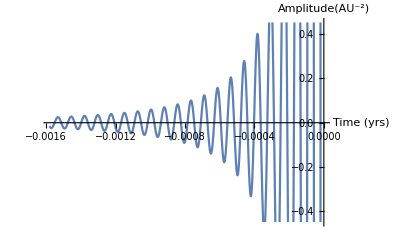

The Scalar field

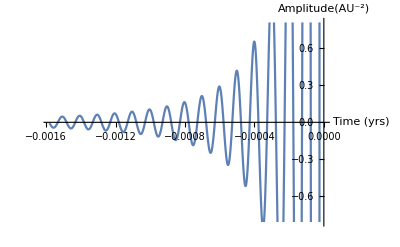

The metric strain

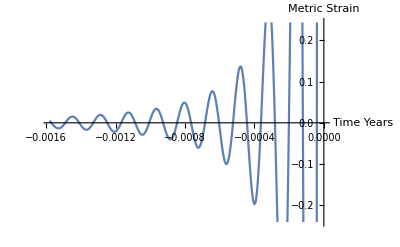

The stress energy invariant

So far these waves clearly have the general form of a gravitational wave.  Now to consider if the modifications of this model are both detectable while not being so great that we would’ve detected them by now.  The method chosen was to compute the resulting percent difference in the stress energy due to the modified and unmodified theory. 

 Stress energy percent difference from unmodified gravity at cosmological scale. Note for the cosmological scale graphs each distance shown would be 1.58 Billion light years.

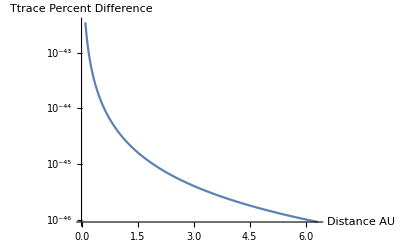

The integrated stress energy at cosmological scales.

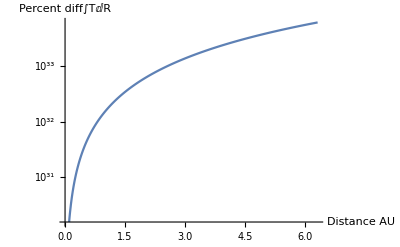

Raw stress energy percent diff at solar system scale.

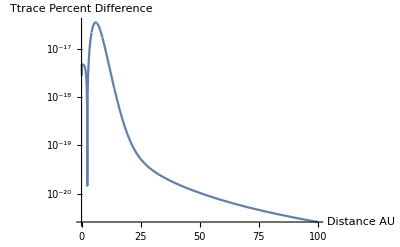

The integrated Stress Energy at solar system scale

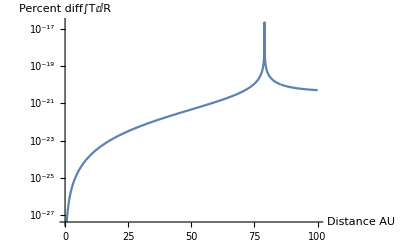

These graphs indicate that all of the solar system test would still hold up in this modified theory regardless of the presence of gravitational waves.

The  invariant of the gravitational wave on the modified background solved for analytically.  A result of not linearizing is a solution that is what MTW describes as “exact”.  Where this wave is present the curvature is not zero.  Everywhere outside the wave the Ricci scalar is exactly zero.  If we set the magnitude of the Ricci wave to zero as well as the cosmological constant then there is no gravitational wave.  These waves carry energy and momentum and like all other forms of energy and momentum they curve space time.

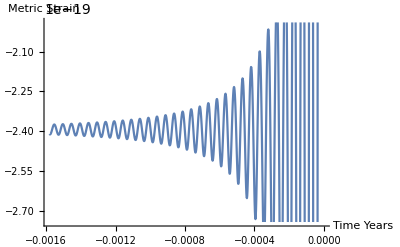

## References

## For our modified Gravity.

To solve for gravitational waves in this case and get a full analytical solution requires first solving for the static Λ vacuum with the above modifications.  The Schwarzschild-DeSitter solution with a minimal modification should satisfy our requirements.  We need a solution which will revert to unmodified Schwarzschild-DeSitter if β is zero, and to Schwarzschild if Λ is zero.

```mathematica
f[r_]:=1-(2G M)/r-(Λ +β Λ^2)/3 r^2
```

Be careful not to confuse f(r) and F(R).  One is a function of the radial coordinate r.  The other is a function of the Ricci scalar R.

```mathematica
({{-f[r], 0, 0, 0}, {0, (f[r])^-1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2(Sin[θ])^2}})//FullSimplify//TeXForm
```

\left(
\begin{array}{cccc}
 \frac{2 G M}{r}+\frac{1}{3} \Lambda  r^2 (\beta  \Lambda +1)-1 & 0 & 0 & 0 \\
 0 & -\frac{3 r}{6 G M+\Lambda  r^3 (\beta  \Lambda +1)-3 r} & 0 & 0 \\
 0 & 0 & r^2 & 0 \\
 0 & 0 & 0 & r^2 \sin ^2(\theta ) \\
\end{array}
\right)

Ricci Tensor

```mathematica
({{1/2 f[r](2 f'[r]/r+f''[r]), 0, 0, 0}, {0, (2f'[r]+r f''[r])/(2r f[r]), 0, 0}, {0, 0, 1-f[r]-r f'[r], 0}, {0, 0, 0, -(Sin[θ])^2(1-f[r]-r f'[r])}})//FullSimplify//MatrixForm
```

Ricci Scalar

```mathematica
Tr[({{-f[r], 0, 0, 0}, {0, (f[r])^-1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2(Sin[θ])^2}}).({{1/2 f[r](2 f'[r]/r+f''[r]), 0, 0, 0}, {0, (2f'[r]+r f''[r])/(2r f[r]), 0, 0}, {0, 0, 1-f[r]-r f'[r], 0}, {0, 0, 0, -(Sin[θ])^2(1-f[r]-r f'[r])}})]//FullSimplify
```

This gives us the background space-time on which we will solve for gravitational waves.

#### The modified Schwarzschild-DeSitter Metric

At this point we now reconsider the background metric.  This metric will provide the killing vectors that will appear in the solution.

f(r)=1-(2G M)/r-(Λ+β Λ^2)/3 r^2

With this function if Λ equals zero we get the Schwarzschild vacuum, if β equal zero but Λ is not then we get the unmodified Schwarzschild-DeSitter space time.

g^μν=(-f(r) | 0 | 0 | 0
0 | (f(r))^-1 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin^2 θ )

For the computer.

```mathematica
g=({{-(1-(2G M)/r-(Λ+β Λ^2)/3 r^2), 0, 0, 0}, {0, (1-(2G M)/r-(Λ+β Λ^2)/3 r^2)^-1, 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2(Sin[θ])^2}})
```

```mathematica
σ= g .{t,r,θ,ϕ}.{t,r,θ,ϕ}
```

The helical killing vector in this modified theory will be.

```mathematica
Subscript[k, μ]={(-(1-(2G M)/r-(Λ+β Λ^2)/3 r^2)),0,0,Ω r^2 (Sin[θ])^2}
```

```mathematica
k^μ={1,0,0,Ω}
```

Set::write: Tag Power in k^μ is Protected.

{1,0,0,Ω}

```mathematica
Subscript[K, μ]=Subscript[k, μ]/(k^μ Subscript[k, μ])
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{k^-μ,Indeterminate,Indeterminate,k^-μ}

```mathematica
{(-(1-(2G M)/r-(Λ+β Λ^2)/3 r^2)),0,0,Ω r^2 (Sin[θ])^2}/({1,0,0,Ω}.{(-(1-(2G M)/r-(Λ+β Λ^2)/3 r^2)),0,0,Ω r^2 (Sin[θ])^2})
```

```mathematica
({(-(1-(2G M)/r-(Λ+β Λ^2)/3 r^2)),0,0,Ω r^2 (Sin[θ])^2}/({1,0,0,Ω}.{(-(1-(2G M)/r-(Λ+β Λ^2)/3 r^2)),0,0,Ω r^2 (Sin[θ])^2})).{dt,dr,dθ,dϕ}//FullSimplify
```

Now to take the indicated integrals∫K_μ ⅆ x^μ

```mathematica
∫(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2))/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆϕ//FullSimplify
```

Now we can write the full solution

```mathematica
1/(4 π^2 σ)(R0 Exp[-ⅈ ω(∫(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2))/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆϕ) ]+R1 Exp[ⅈ ω(∫(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2))/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆϕ) ])//FullSimplify
```

```mathematica
Ricci=(3 ⅇ^(-(ⅈ ω (t (24 π^2-3 r+r^3 Λ (1+β Λ))+3 r^3 ϕ Ω Sin[θ]^2))/(24 π^2-3 r+r^3 Λ (1+β Λ)+3 r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (t (24 π^2-3 r+r^3 Λ (1+β Λ))+3 r^3 ϕ Ω Sin[θ]^2))/(24 π^2-3 r+r^3 Λ (1+β Λ)+3 r^3 Ω^2 Sin[θ]^2)) R1) (24 π^2-3 r+r^3 Λ (1+β Λ)))/(4 π^2 (576 π^4 t^2-144 π^2 r t^2+9 r^2 t^2+r^6 Λ (1+β Λ) (3 θ^2+t^2 Λ (1+β Λ))+24 π^2 r^3 (3 θ^2+2 t^2 Λ (1+β Λ))-3 r^4 (3+3 θ^2+2 t^2 Λ (1+β Λ))+3 r^3 (24 π^2-3 r+r^3 Λ (1+β Λ)) ϕ^2 Sin[θ]^2))
```

Now for the scalar field.

```mathematica
1/(4 π^2 σ)(ϕ0 Exp[-ⅈ ω(∫(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2))/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆϕ) +ξ Ricci]+ϕ1 Exp[ⅈ ω(∫(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2))/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆt+∫(r^2 Ω Sin[θ]^2)/(-1+(2 G M)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)ⅆϕ)+ξ Ricci ])
```

```mathematica
Phifield=(ⅇ^((3 ⅇ^(-(ⅈ ω (t (24 π^2-3 r+r^3 Λ (1+β Λ))+3 r^3 ϕ Ω Sin[θ]^2))/(24 π^2-3 r+r^3 Λ (1+β Λ)+3 r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (t (24 π^2-3 r+r^3 Λ (1+β Λ))+3 r^3 ϕ Ω Sin[θ]^2))/(24 π^2-3 r+r^3 Λ (1+β Λ)+3 r^3 Ω^2 Sin[θ]^2)) R1) (24 π^2-3 r+r^3 Λ (1+β Λ)) ξ)/(4 π^2 (576 π^4 t^2-144 π^2 r t^2+9 r^2 t^2+r^6 Λ (1+β Λ) (3 θ^2+t^2 Λ (1+β Λ))+24 π^2 r^3 (3 θ^2+2 t^2 Λ (1+β Λ))-3 r^4 (3+3 θ^2+2 t^2 Λ (1+β Λ))+3 r^3 (24 π^2-3 r+r^3 Λ (1+β Λ)) ϕ^2 Sin[θ]^2))-ⅈ ω (-t/(-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2))+(r^2 t (Λ+β Λ^2))/(3 (-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2))) ϕ0+ⅇ^((3 ⅇ^(-(ⅈ ω (t (24 π^2-3 r+r^3 Λ (1+β Λ))+3 r^3 ϕ Ω Sin[θ]^2))/(24 π^2-3 r+r^3 Λ (1+β Λ)+3 r^3 Ω^2 Sin[θ]^2)) r (R0+ⅇ^((2 ⅈ ω (t (24 π^2-3 r+r^3 Λ (1+β Λ))+3 r^3 ϕ Ω Sin[θ]^2))/(24 π^2-3 r+r^3 Λ (1+β Λ)+3 r^3 Ω^2 Sin[θ]^2)) R1) (24 π^2-3 r+r^3 Λ (1+β Λ)) ξ)/(4 π^2 (576 π^4 t^2-144 π^2 r t^2+9 r^2 t^2+r^6 Λ (1+β Λ) (3 θ^2+t^2 Λ (1+β Λ))+24 π^2 r^3 (3 θ^2+2 t^2 Λ (1+β Λ))-3 r^4 (3+3 θ^2+2 t^2 Λ (1+β Λ))+3 r^3 (24 π^2-3 r+r^3 Λ (1+β Λ)) ϕ^2 Sin[θ]^2))+ⅈ ω (-t/(-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2)+(8 π^2 t)/(r (-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2))+(r^2 t (Λ+β Λ^2))/(3 (-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2))+(r^2 ϕ Ω Sin[θ]^2)/(-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2)+r^2 Ω^2 Sin[θ]^2))) ϕ1)/(4 π^2 (r^2 θ^2+r^2/(1-(8 π^2)/r-1/3 r^2 (Λ+β Λ^2))+t^2 (-1+(8 π^2)/r+1/3 r^2 (Λ+β Λ^2))+r^2 ϕ^2 Sin[θ]^2))
```

Now we need to check the limits at the origin and at infinity.  This needs to be finite at both.

```mathematica
Limit[{Ricci,Phifield}, r->0]//FullSimplify
```

$Aborted

```mathematica
Limit[{Ricci,Phifield}, r->∞]//FullSimplify
```

{0,0}

This shows the gravitational wave Ricci goes to a constant the value of which will shrink as the amplitude of the EMRI orbit increases.   Meanwhile the same is for Phifield.   The boundary at infinity and the initial values being satisfied the solution for this system of equations, in Schwarzschild space time can be written as follows.

```mathematica
Ricci//TraditionalForm
```

(3 r (Λ r^3 (β Λ+1)-3 r+24 π^2) exp(-(ⅈ ω (3 r^3 Ω ϕ sin^2(θ)+t (Λ r^3 (β Λ+1)-3 r+24 π^2)))/(Λ r^3 (β Λ+1)+3 r^3 Ω^2 sin^2(θ)-3 r+24 π^2)) (R0+R1 exp((2 ⅈ ω (3 r^3 Ω ϕ sin^2(θ)+t (Λ r^3 (β Λ+1)-3 r+24 π^2)))/(Λ r^3 (β Λ+1)+3 r^3 Ω^2 sin^2(θ)-3 r+24 π^2))))/(4 π^2 (Λ r^6 (β Λ+1) (3 θ^2+Λ t^2 (β Λ+1))-3 r^4 (3 θ^2+2 Λ t^2 (β Λ+1)+3)+3 r^3 ϕ^2 sin^2(θ) (Λ r^3 (β Λ+1)-3 r+24 π^2)+24 π^2 r^3 (3 θ^2+2 Λ t^2 (β Λ+1))+9 r^2 t^2-144 π^2 r t^2+576 π^4 t^2))

```mathematica
Phifield//TraditionalForm
```

(ⅇ^((3 ⅇ^(-(ⅈ ω (3 ϕ Ω sin^2(θ) r^3+t (Λ (β Λ+1) r^3-3 r+24 π^2)))/(3 Ω^2 sin^2(θ) r^3+Λ (β Λ+1) r^3-3 r+24 π^2)) r (R0+ⅇ^((2 ⅈ ω (3 ϕ Ω sin^2(θ) r^3+t (Λ (β Λ+1) r^3-3 r+24 π^2)))/(3 Ω^2 sin^2(θ) r^3+Λ (β Λ+1) r^3-3 r+24 π^2)) R1) (Λ (β Λ+1) r^3-3 r+24 π^2) ξ)/(4 π^2 (Λ (β Λ+1) (Λ (β Λ+1) t^2+3 θ^2) r^6-3 (2 Λ (β Λ+1) t^2+3 θ^2+3) r^4+3 (Λ (β Λ+1) r^3-3 r+24 π^2) ϕ^2 sin^2(θ) r^3+24 π^2 (2 Λ (β Λ+1) t^2+3 θ^2) r^3+9 t^2 r^2-144 π^2 t^2 r+576 π^4 t^2))-ⅈ ω ((ϕ Ω sin^2(θ) r^2)/(Ω^2 sin^2(θ) r^2+1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r)+(t (β Λ^2+Λ) r^2)/(3 (Ω^2 sin^2(θ) r^2+1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r))-t/(Ω^2 sin^2(θ) r^2+1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r)+(8 π^2 t)/((Ω^2 sin^2(θ) r^2+1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r) r))) ϕ0+ⅇ^((3 ⅇ^(-(ⅈ ω (3 ϕ Ω sin^2(θ) r^3+t (Λ (β Λ+1) r^3-3 r+24 π^2)))/(3 Ω^2 sin^2(θ) r^3+Λ (β Λ+1) r^3-3 r+24 π^2)) r (R0+ⅇ^((2 ⅈ ω (3 ϕ Ω sin^2(θ) r^3+t (Λ (β Λ+1) r^3-3 r+24 π^2)))/(3 Ω^2 sin^2(θ) r^3+Λ (β Λ+1) r^3-3 r+24 π^2)) R1) (Λ (β Λ+1) r^3-3 r+24 π^2) ξ)/(4 π^2 (Λ (β Λ+1) (Λ (β Λ+1) t^2+3 θ^2) r^6-3 (2 Λ (β Λ+1) t^2+3 θ^2+3) r^4+3 (Λ (β Λ+1) r^3-3 r+24 π^2) ϕ^2 sin^2(θ) r^3+24 π^2 (2 Λ (β Λ+1) t^2+3 θ^2) r^3+9 t^2 r^2-144 π^2 t^2 r+576 π^4 t^2))+ⅈ ω ((ϕ Ω sin^2(θ) r^2)/(Ω^2 sin^2(θ) r^2+1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r)+(t (β Λ^2+Λ) r^2)/(3 (Ω^2 sin^2(θ) r^2+1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r))-t/(Ω^2 sin^2(θ) r^2+1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r)+(8 π^2 t)/((Ω^2 sin^2(θ) r^2+1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r) r))) ϕ1)/(4 π^2 (θ^2 r^2+ϕ^2 sin^2(θ) r^2+r^2/(-1/3 (β Λ^2+Λ) r^2+1-(8 π^2)/r)+t^2 (1/3 (β Λ^2+Λ) r^2-1+(8 π^2)/r)))

### Computer Algebra Solution

To be certain the above math is  correct we now demonstrate a solution which is found via the Mathematica computer algebra system.  It is as simple as putting the derivatives and killing vectors etc into a form which Mathematica can interpret and simplify by hand.   I will also leave the gravitational wave arbitrary.  The result will give a solution up to an integral. 

For simplicity the dependence of R on ϕ^2 will be ignored as it is presumed ϕ is small.

(□- 1/(6 β)+ξ/(6 β) ϕ^2)R-ξ/(2β) □ϕ^2 =κ^2/(6 β)T

```mathematica
DSolve[{D[u[t,r,θ,ϕ],t]+Ω/(r Sin[θ]) D[u[t,r,θ,ϕ],ϕ]==(-ⅈ ω+1/(6 β))u[t,r,θ,ϕ]},u[t,r,θ,ϕ],{t,r,θ,ϕ}]
```

```mathematica
DSolve[{D[u[t,r,θ,ϕ],t]+Ω/(r Sin[θ]) D[u[t,r,θ,ϕ],ϕ]==(ⅈ ω+1/(6 β))u[t,r,θ,ϕ]},u[t,r,θ,ϕ],{t,r,θ,ϕ}]
```

The solutions that the computer finds  is similar to that found by hand up to an integral over the Ricci scalar with a arbitrary function of r,θ and ϕ.  The simplest function that can satisfy the boundary conditions at infinity, and be compatible with theoretical expectation  is almost given in the solution.  We will modify it a bit to ensure that it stays finite at all values of the variables.   

(r ϕ-t Ω Csc[θ]θ)/r^2

```mathematica
Rcas=(ⅇ^(1/6 t (1/β-6 ⅈ ω)) (R0+ⅇ^(2 ⅈ t ω) R1) (r ϕ-t θ Ω Csc[θ]))/r^2
```

Now to Solve for ϕ ...

```mathematica
DSolve[{D[f[t,r,θ,ϕ],t]+Ω/(r Sin[θ]) D[f[t,r,θ,ϕ],ϕ]==(-ⅈ ω+ξ ((ⅇ^(1/6 t (1/β-6 ⅈ ω)) (R0+ⅇ^(2 ⅈ t ω) R1) (r ϕ-t θ Ω Csc[θ]))/r^2))f[t,r,θ,ϕ]},f[t,r,θ,ϕ],{t,r,θ,ϕ}]
```

```mathematica
DSolve[{D[f[t,r,θ,ϕ],t]+Ω/(r Sin[θ]) D[f[t,r,θ,ϕ],ϕ]==(ⅈ ω+ξ ((ⅇ^(1/6 t (1/β-6 ⅈ ω)) (R0+ⅇ^(2 ⅈ t ω) R1) (r ϕ-t θ Ω Csc[θ]))/r^2))f[t,r,θ,ϕ]},f[t,r,θ,ϕ],{t,r,θ,ϕ}]
```

With these findings the computer algebra solutions can be written down

R=(ⅇ^(1/6 t (1/β-6 ⅈ ω)) (R0+ⅇ^(2 ⅈ t ω) R1) (r ϕ-t θ Ω Csc[θ]))/r^2

ϕ=(r ϕ-t Ω Csc[θ]θ)/r^2(ϕ0 ⅇ^(-ⅈ t ω-(6 ⅇ^(1/6 t (1/β-6 ⅈ ω)) β (-1+θ) ξ ((ⅇ^(2 ⅈ t ω) R1 (6 β+t (-1-6 ⅈ β ω)))/(ⅈ-6 β ω)^2+(R0 (6 β+t (-1+6 ⅈ β ω)))/(ⅈ+6 β ω)^2) Ω Csc[θ])/r^2+(6 ⅇ^(1/6 t (1/β-6 ⅈ ω)) β ξ (R0+6 ⅈ R0 β ω+ⅇ^(2 ⅈ t ω) R1 (1-6 ⅈ β ω)) (r ϕ-t Ω Csc[θ]))/(r^2 (1+36 β^2 ω^2))) + ϕ1 ⅇ^(ⅈ t ω-(6 ⅇ^(1/6 t (1/β-6 ⅈ ω)) β (-1+θ) ξ ((ⅇ^(2 ⅈ t ω) R1 (6 β+t (-1-6 ⅈ β ω)))/(ⅈ-6 β ω)^2+(R0 (6 β+t (-1+6 ⅈ β ω)))/(ⅈ+6 β ω)^2) Ω Csc[θ])/r^2+(6 ⅇ^(1/6 t (1/β-6 ⅈ ω)) β ξ (R0+6 ⅈ R0 β ω+ⅇ^(2 ⅈ t ω) R1 (1-6 ⅈ β ω)) (r ϕ-t Ω Csc[θ]))/(r^2 (1+36 β^2 ω^2))))

This set of equations matches the major features of the solution found above and differs only in the simplifying assumptions needed to make the math doable by Mathematica.   This gives me confidence that the math was done correctly by hand.

### Computer Assisted Evaluation Of Integrals (Deprecated)

The solution for the field equations found by the analytical method above contains a set of integrals that while doable would be tedious with many steps.   In particular ∫k_μ ⅆ x^μ  and ∫K_μ(ⅈ ω+ξ R)ⅆ x^μ etc.

R=1/(4 π^2 σ(x_1,x_2))(R_0 Exp[-ⅈ ω ∫k_μ ⅆ x^μ]+R_1 Exp[ⅈ ω ∫k_μ ⅆ x^μ])

ϕ=1/(4 π^2 σ(x_1,x_2))(ϕ_0 Exp[∫K_μ(- ⅈ ω+ξ R)ⅆ x^μ ]+ϕ_1 Exp[∫K_μ(ⅈ ω+ξ R)ⅆ x^μ ])

The above equations have the virtues of being stated in terms of invariants and in coordinate free form.  Thus they satisfy all the requirements of General Relativity.  The computer algebra system Mathematica does not care about this important fact.  To encode this into the math we must choose a coordinate system and specify the normalized helical killing vector  K_μ in it.  Naturally the problem has spherical symmetry so spherical coordinates are used. 

In an earlier iteration of this work the unmodified Schwarzschild solution was used this allowed us to establish a basic intuitive sense of the physics of this soulution.  However, it is desirable to have a modified Schwarzschild like solution for the static case.

1	 Starobinsky, A. A. (December 1979). "Spectrum Of Relict Gravitational Radiation And The Early State Of The Universe". Journal of Experimental and Theoretical Physics Letters. 30: 682. Bibcode:1979JETPL..30..682S.; Starobinskii, A. A. (December 1979). "Spectrum of relict gravitational radiation and the early state of the universe". Pisma Zh. Eksp. Teor. Fiz. (Soviet Journal of Experimental and Theoretical Physics Letters). 30: 719. Bibcode:1979ZhPmR..30..719S.  http://www.jetpletters.ru/ps/1370/article_20738.pdf

2	Starobinsky, A.A (1980). "A new type of isotropic cosmological models without singularity". Physics Letters B. 91 (1): 99–102. Bibcode:1980PhLB...91...99S. doi:10.1016/0370-2693(80)90670-X

3	Hu, Wayne; Barkana, Rennan; Gruzinov, Andrei (2000). "Cold and Fuzzy Dark Matter". Physical Review Letters. 85 (6): 1158–61. arXiv:astro-ph/0003365. Bibcode:2000PhRvL..85.1158H. doi:10.1103/PhysRevLett.85.1158. PMID 10991501.

4	Duffy, Leanne D.; van Bibber, Karl (2009). "Axions as dark matter particles". New Journal of Physics. 11 (10): 105008. arXiv:0904.3346. Bibcode:2009NJPh...11j5008D. doi:10.1088/1367-2630/11/10/105008. S2CID 17212949.

5	@ARTICLE{2017PhRvD..95h4025P,
       author = {{Pravda}, V. and {Pravdov{\'a}}, A. and {Podolsk{\'y}}, J. and {{\v{S}}varc}, R.},
        title = "{Exact solutions to quadratic gravity}",
      journal = {\prd},
     keywords = {General Relativity and Quantum Cosmology},
         year = 2017,
        month = apr,
       volume = {95},
       number = {8},
          eid = {084025},
        pages = {084025},
          doi = {10.1103/PhysRevD.95.084025},
archivePrefix = {arXiv},
       eprint = {1606.02646},
 primaryClass = {gr-qc},
       adsurl = {https://ui.adsabs.harvard.edu/abs/2017PhRvD..95h4025P},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

6	@ARTICLE{2011PhRvD..84f2003C,
       author = {{Cornish}, Neil and {Sampson}, Laura and {Yunes}, Nicol{\'a}s and {Pretorius}, Frans},
        title = "{Gravitational wave tests of general relativity with the parameterized post-Einsteinian framework}",
      journal = {\prd},
     keywords = {04.80.Cc, 04.30.-w, 04.50.Kd, 04.80.Nn, Experimental tests of gravitational theories, Gravitational waves: theory, Modified theories of gravity, Gravitational wave detectors and experiments, General Relativity and Quantum Cosmology, Astrophysics - High Energy Astrophysical Phenomena},
         year = 2011,
        month = sep,
       volume = {84},
       number = {6},
          eid = {062003},
        pages = {062003},
          doi = {10.1103/PhysRevD.84.062003},
archivePrefix = {arXiv},
       eprint = {1105.2088},
 primaryClass = {gr-qc},
       adsurl = {https://ui.adsabs.harvard.edu/abs/2011PhRvD..84f2003C},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

7	@ARTICLE{2021PhRvD.104f4047K,
       author = {{Katz}, Michael L. and {Chua}, Alvin J.~K. and {Speri}, Lorenzo and {Warburton}, Niels and {Hughes}, Scott A.},
        title = "{Fast extreme-mass-ratio-inspiral waveforms: New tools for millihertz gravitational-wave data analysis}",
      journal = {\prd},
     keywords = {General Relativity and Quantum Cosmology},
         year = 2021,
        month = sep,
       volume = {104},
       number = {6},
          eid = {064047},
        pages = {064047},
          doi = {10.1103/PhysRevD.104.064047},
archivePrefix = {arXiv},
       eprint = {2104.04582},
 primaryClass = {gr-qc},
       adsurl = {https://ui.adsabs.harvard.edu/abs/2021PhRvD.104f4047K},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

8	C Q Geng, Gravitational Waves in Viable Modified Gravity
Theories 2012 J.Phys.:Conf.Ser.384 012030 https://ui.adsabs.harvard.edu/abs/2012JPhCS.384a2030G

9	 Diego Fernández-Silvestre, Joshua Foo, and Michael R. R. Good. On the duality of Schwarzschild-de Sitter spacetime and moving mirror.  Classical and Quantum Gravity,
39(5):055006, March 2022.

10	@ARTICLE{2019A&A...627A..92G,
       author = {{Gourgoulhon}, E. and {Le Tiec}, A. and {Vincent}, F.~H. and {Warburton}, N.},
        title = "{Gravitational waves from bodies orbiting the Galactic center black hole and their detectability by LISA}",
      journal = {\aap},
     keywords = {gravitational waves, black hole physics, Galaxy: center, stars: low-mass, brown dwarfs, stars: black holes, General Relativity and Quantum Cosmology, Astrophysics - High Energy Astrophysical Phenomena, Astrophysics - Solar and Stellar Astrophysics},
         year = 2019,
        month = jul,
       volume = {627},
          eid = {A92},
        pages = {A92},
          doi = {10.1051/0004-6361/201935406},
archivePrefix = {arXiv},
       eprint = {1903.02049},
 primaryClass = {gr-qc},
       adsurl = {https://ui.adsabs.harvard.edu/abs/2019A&A...627A..92G},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

11	@ARTICLE{2017AJ....153..121P,
       author = {{Park}, Ryan S. and {Folkner}, William M. and {Konopliv}, Alexander S. and {Williams}, James G. and {Smith}, David E. and {Zuber}, Maria T.},
        title = "{Precession of Mercury{	extquoteright}s Perihelion from Ranging to the MESSENGER Spacecraft}",
      journal = {\aj},
     keywords = {astrometry, celestial mechanics, ephemerides, planets and satellites: individual: Mercury, relativistic processes, Sun: interior},
         year = 2017,
        month = mar,
       volume = {153},
       number = {3},
          eid = {121},
        pages = {121},
          doi = {10.3847/1538-3881/aa5be2},
       adsurl = {https://ui.adsabs.harvard.edu/abs/2017AJ....153..121P},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

12	@ARTICLE{1947RvMP...19..361C,
       author = {{Clemence}, G.~M.},
        title = "{The Relativity Effect in Planetary Motions}",
      journal = {Reviews of Modern Physics},
         year = 1947,
        month = oct,
       volume = {19},
       number = {4},
        pages = {361-364},
          doi = {10.1103/RevModPhys.19.361},
       adsurl = {https://ui.adsabs.harvard.edu/abs/1947RvMP...19..361C},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

13	@ARTICLE{2017AJ....153..121P,
       author = {{Park}, Ryan S. and {Folkner}, William M. and {Konopliv}, Alexander S. and {Williams}, James G. and {Smith}, David E. and {Zuber}, Maria T.},
        title = "{Precession of Mercury{	extquoteright}s Perihelion from Ranging to the MESSENGER Spacecraft}",
      journal = {\aj},
     keywords = {astrometry, celestial mechanics, ephemerides, planets and satellites: individual: Mercury, relativistic processes, Sun: interior},
         year = 2017,
        month = mar,
       volume = {153},
       number = {3},
          eid = {121},
        pages = {121},
          doi = {10.3847/1538-3881/aa5be2},
       adsurl = {https://ui.adsabs.harvard.edu/abs/2017AJ....153..121P},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

14	@ARTICLE{1947RvMP...19..361C,
       author = {{Clemence}, G.~M.},
        title = "{The Relativity Effect in Planetary Motions}",
      journal = {Reviews of Modern Physics},
         year = 1947,
        month = oct,
       volume = {19},
       number = {4},
        pages = {361-364},
          doi = {10.1103/RevModPhys.19.361},
       adsurl = {https://ui.adsabs.harvard.edu/abs/1947RvMP...19..361C},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

15	@ARTICLE{2009ApJ...699.1395F,
       author = {{Fomalont}, E. and {Kopeikin}, S. and {Lanyi}, G. and {Benson}, J.},
        title = "{Progress in Measurements of the Gravitational Bending of Radio Waves Using the VLBA}",
      journal = {\apj},
     keywords = {gravitation, quasars: individual: 3C279, relativity, techniques: interferometric, Astrophysics - Cosmology and Extragalactic Astrophysics},
         year = 2009,
        month = jul,
       volume = {699},
       number = {2},
        pages = {1395-1402},
          doi = {10.1088/0004-637X/699/2/1395},
archivePrefix = {arXiv},
       eprint = {0904.3992},
 primaryClass = {astro-ph.CO},
       adsurl = {https://ui.adsabs.harvard.edu/abs/2009ApJ...699.1395F},
      adsnote = {Provided by the SAO/NASA Astrophysics Data System}
}

Let θ=ω∫k_μ ⅆ x^μ  We can use these to give a basis inspired by the Pauli matrices

```mathematica
Θ
```

This also results in the matrix found in our solutions.   Now let us consider that the Ricci scalar will be the contraction of a metric with a Ricci curvature tensor.  We can factor out what the metric for the gravitational wave would be.

R̃=1/(4 π^2 σ(x_1,x_2))Tr[(R_0 | 0
0 | R_1)(e^(-ⅈω∫k_μ ⅆ x^μ) | 0
0 | e^(ⅈω∫k_μ ⅆ x^μ))](e^(∫k_μ(- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

R̃=1/(4 π^2 σ(x_1,x_2))Tr[(R_0 | 0
0 | R_1)(ⅇ^(-ⅈ/2ω∫k_μ ⅆ x^μ) | 0
0 | ⅇ^(ⅈ/2 ω∫k_μ ⅆ x^μ))(ⅇ^(-ⅈ/2ω∫k_μ ⅆ x^μ) | 0
0 | ⅇ^(ⅈ/2 ω∫k_μ ⅆ x^μ))](e^(∫k_μ(- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

1/(4 π^2 σ(x_1,x_2))Tr[(R_0 | 0
0 | R_1)(ⅇ^(-ⅈ/2ω∫k_μ ⅆ x^μ) | 0
0 | ⅇ^(ⅈ/2 ω∫k_μ ⅆ x^μ))(ⅇ^(-ⅈ/2ω∫k_μ ⅆ x^μ) | 0
0 | ⅇ^(ⅈ/2 ω∫k_μ ⅆ x^μ))](e^(∫k_μ(- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

There fore we can define the following for the metric, Ricci tensor, and the scalar field.

g^μν=1/(√(4 π^2 σ(x_1,x_2)))(ⅇ^(-ⅈ/2ω∫k_μ ⅆ x^μ) | 0
0 | ⅇ^(ⅈ/2 ω∫k_μ ⅆ x^μ))

R_μν=1/(√(4 π^2 σ(x_1,x_2)))(R_0 | 0
0 | R_1)(ⅇ^(-ⅈ/2ω∫k_μ ⅆ x^μ) | 0
0 | ⅇ^(ⅈ/2 ω∫k_μ ⅆ x^μ))(e^(∫k_μ(- ξ/(6 β)ϕ^2[R]±1/g_i √((κ^2 T)/(6 β)- ξ/(6 β)ϕ^2[R]))ⅆ x^μ))

ϕ̂=1/(√(4 π^2 σ(x_1,x_2)))(ϕ_0 | 0
0 | ϕ_1)(ⅇ^(-ⅈ/2ω∫k_μ ⅆ x^μ) | 0
0 | ⅇ^(ⅈ/2 ω∫k_μ ⅆ x^μ))e^(ξ∫k_μ Rⅆ x^μ)

More importantly we find the form of the metric strain which is what our instruments will observe.

```mathematica
g^μν Subscript[g, μν]=1/(4 π^2 σ(Subscript[x, 1],Subscript[x, 2]))Tr[({{ⅇ^(-ⅈ/2 ω∫Subscript[k, μ] ⅆ x^μ), 0}, {0, ⅇ^(ⅈ/2 ω∫Subscript[k, μ] ⅆ x^μ)}})({{ⅇ^(-ⅈ/2 ω∫Subscript[k, μ] ⅆ x^μ), 0}, {0, ⅇ^(ⅈ/2 ω∫Subscript[k, μ] ⅆ x^μ)}})]
```